### Add graphics row and fix viewpoint on old non-panels

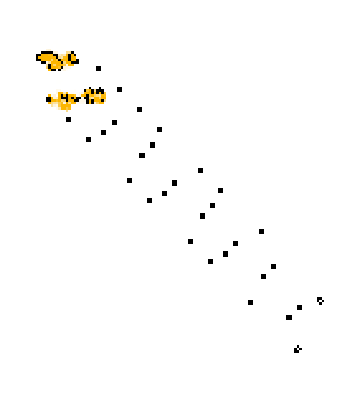
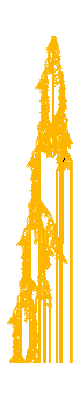
{-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
{CellularAutomatonHistoryPlot["GameOfLife",{Transpose@SparseArray[…],0},1100,Mesh->False],CellularAutomatonSpacetimePlot["GameOfLife",{Transpose@SparseArray[…],0},400,Mesh->None,"Decay"->.99],CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},200]}
```

```mathematica
GraphicsRow[{CellularAutomatonHistoryPlot["GameOfLife",{Transpose@SparseArray[…],0},1100,Mesh->False],CellularAutomatonSpacetimePlot["GameOfLife",{Transpose@SparseArray[…],0},400,Mesh->None,"Decay"->.99],CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},200, ViewPoint->{1.3,2.4,1.8}]}, ImageSize->{Automatic, 250}]
```

-Graphics-

### Make bar chart lighter blue

```mathematica
ld = {{"[◼]", "Data"}}["$LifeData"];
```

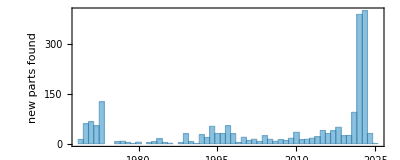

```mathematica
With[{ld = {{"[◼]", "Data"}}["$LifeData"]}, Histogram[Flatten[
Table[#[[1]],#[[2]]]&/@Normal[KeySort[(Total/@Map[Last,GroupBy[KeyValueMap[{ld[#1]["Year"],Count[#2,None]}&,xresall],First],{2}])~Join~<|Thread[{1974,1975,1981,1987}->0]|>]]],50,AspectRatio->.4,Frame->True,FrameLabel->{None,"new parts found"},PlotRange->All, TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],ChartStyle->Directive[Opacity[.6,ColorData["DefaultPlotColors"][1]],EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]]]]]
```

### Remove extra branches

```mathematica
byp=SortBy[(SortBy[#,#Year&]&/@GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&&MemberQ[{2,3,4,5,6,7,8,9,10,12,15,16,20,21,30,36}, #["Period"]] &]],#Period&]),#[[1,"Period"]]&];
```

```mathematica
Style[Row[Labeled[GraphicsRow[Labeled[First[WeaklyConnectedGraphComponents[BoundingBoxLayeredGraph[#, Automatic, ImageSize-> {If[#Period == 30, 50, Automatic], 100}]]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@# (*ImageSize->{{20,300},{10,100}}*)],Style[Text["period "<>ToString@#[[1]]["Period"]], 10],Left]&/@(DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#)&[byp],Graphics[Style[Line[{{0,-1},{0,1}}],GrayLevel[.8]],PlotRange->{{-.1,.1},{-1,1}},ImageSize->{12,60}]],LineSpacing->{1,1}]
```

-Graphics--Graphics-period 2-Graphics-period 3-Graphics-period 4-Graphics-period 5-Graphics-period 6-Graphics-period 7-Graphics-period 8-Graphics-period 9-Graphics-period 10-Graphics-period 12-Graphics-period 15-Graphics-period 16-Graphics-period 20-Graphics-period 21-Graphics-period 30-Graphics-period 36

### Perhaps Willem can figure out how to include a Callout.

```mathematica
(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Gun"&], #Period&])
```

```mathematica
ListPlot[Function[pds,
MapIndexed[
Callout[Style[ {#Year, #Period},If[Last[#2] == 1 || #Name ==="13-engine Cordership",Red, If[Last[#2] == Length[pds], RGBColor[0.24, 0.6, 0.8], None]]], If[Times@@Dimensions[#MatrixData]>2000, None, CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10, ImageSize->{30, 30}, Mesh->False, FrameStyle->Opacity[.3]]]]&
, pds]]/@ ((SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Gun"&], #Period&])), Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log",PlotStyle-> Directive[Lighter[Gray], PointSize[.01]],
Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],Dotted,HalfLine[{#Year,Log[#Period]},{-1,0}]&/@(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Gun"&], #Period&])[[All, -1]]}),
PlotRangePadding->{{1, 1}, {Automatic, .25}}]
```

-Graphics-

### Test

```mathematica
Export[NotebookDirectory[]<>"test.gif",CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Breeder 1"]["MatrixData"],0},300,Mesh->None], "GIF"]
```

/Users/erichegonzales/Documents/Projects/Wolfram/GameOfLife/test.gif